```mathematica
SystemInformation[]
```

1234567

```mathematica
$Assumptions={t4∈Arrays[{n,n,n,n}, Reals,Symmetric[{1,2}]]};
```

```mathematica
(*Explicitly,I have constructed two tensors that should be the same when symmetrised in the first two indices. That is these two:*)
```

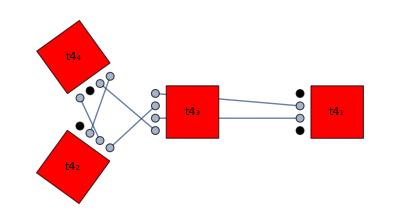
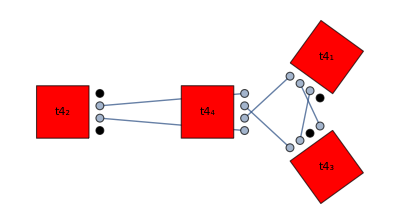

```mathematica
twoTensors={TensorTranspose[TensorContract[t4 ⊗ t4 ⊗ t4 ⊗ t4, {{2, 10}, {3, 12}, {6, 13}, {7, 16}, {8, 11}, {9, 14}}], {1, 4, 2, 3}], 
 TensorTranspose[TensorContract[t4 ⊗ t4 ⊗ t4 ⊗ t4, {{2, 10}, {3, 12}, {4, 15}, {6, 13}, {7, 16}, {9, 14}}], {1, 2, 4, 3}]};

(* Plot these two tensors*)
SymbolicTensors`TensorGraph[#[[1]],Method->2] &/@twoTensors
```

```mathematica
(*But TensorReduce does not identify this. The following should be True.*)
```

```mathematica
Symmetrize[twoTensors[[1]], Symmetric[{1,2}]]==Symmetrize[twoTensors[[2]], Symmetric[{1,2}]]//TensorReduce
```

1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 10
3 | 12
6 | 13
7 | 16
8 | 11
9 | 14)],{1,4,2,3}]+1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 13
3 | 16
4 | 11
6 | 10
7 | 12
9 | 14)],{2,3,4,1}]==1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 10
3 | 12
4 | 15
6 | 13
7 | 16
9 | 14)],{1,2,4,3}]+1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 13
3 | 16
6 | 10
7 | 12
8 | 15
9 | 14)],{1,4,2,3}]

```mathematica
(*I can show explicitly that these two tensors should be symmetric. To do this, I find the symmetries of t4 ⊗ t4 ⊗ t4 ⊗ t4, and apply those first to it, and then perform the contraction.*)
```

```mathematica
getSymmetry =TensorSymmetry[t4 ⊗ t4 ⊗ t4 ⊗ t4]
{t1sym,t2sym,t3sym,t4sym, switch12, switch23, switch34}=First/@getSymmetry
```

(Cycles[(1 | 2)] | 1
Cycles[(5 | 6)] | 1
Cycles[(9 | 10)] | 1
Cycles[(13 | 14)] | 1
Cycles[(1 | 5
2 | 6
3 | 7
4 | 8)] | 1
Cycles[(5 | 9
6 | 10
7 | 11
8 | 12)] | 1
Cycles[(9 | 13
10 | 14
11 | 15
12 | 16)] | 1)

{Cycles[(1 | 2)],Cycles[(5 | 6)],Cycles[(9 | 10)],Cycles[(13 | 14)],Cycles[(1 | 5
2 | 6
3 | 7
4 | 8)],Cycles[(5 | 9
6 | 10
7 | 11
8 | 12)],Cycles[(9 | 13
10 | 14
11 | 15
12 | 16)]}

```mathematica
~
```

TensorTranspose[t4⊗t4⊗t4⊗t4,{5,6,7,8,1,2,3,4,13,14,15,16,9,10,11,12}]

These are indeed symmetries: True

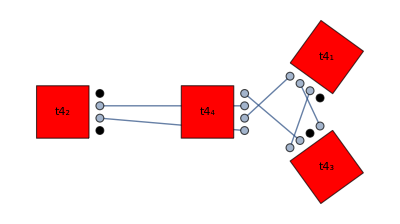

```mathematica
applySymmetries = TensorTranspose[TensorTranspose[t4 ⊗ t4 ⊗ t4 ⊗ t4,switch12],switch34] 
Print["These are indeed symmetries: ",TensorReduce[applySymmetries]===t4 ⊗ t4 ⊗ t4 ⊗ t4];

SymbolicTensors`TensorGraph[#[[1]],Method->2]&@TensorTranspose[TensorContract[applySymmetries, {{2, 10}, {3, 12}, {6, 13}, {7, 16}, {8, 11}, {9, 14}}], {1, 4, 2, 3}]
```

```mathematica
(*These two should have identical output, but do not:*)
```

```mathematica
Symmetrize[twoTensors[[1]]/.t4 ⊗ t4 ⊗ t4 ⊗ t4->applySymmetries, Symmetric[{1,2}]]==Symmetrize[twoTensors[[2]], Symmetric[{1,2}]]//TensorReduce
```

True

```mathematica
Symmetrize[TensorReduce[twoTensors[[1]]/.t4 ⊗ t4 ⊗ t4 ⊗ t4->applySymmetries](*<----The only difference is the new TensorReduce*), Symmetric[{1,2}]]==Symmetrize[twoTensors[[2]], Symmetric[{1,2}]]//TensorReduce
```

1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 10
3 | 12
4 | 15
6 | 13
7 | 16
9 | 14)],{2,3,4,1}]+1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 13
3 | 16
6 | 10
7 | 12
8 | 15
9 | 14)],{1,4,2,3}]==1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 10
3 | 12
4 | 15
6 | 13
7 | 16
9 | 14)],{1,2,4,3}]+1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 13
3 | 16
6 | 10
7 | 12
8 | 15
9 | 14)],{1,4,2,3}]

```mathematica
(*So clearly the canonicalisation in TensorReduce fails here!*)
```

```mathematica
(*Swritten out more explicitly*)
```

```mathematica
Symmetrize[TensorTranspose[TensorContract[applySymmetries, {{2, 10}, {3, 12}, {6, 13}, {7, 16}, {8, 11}, {9, 14}}], {1, 4, 2, 3}], Symmetric[{1,2}]]==Symmetrize[twoTensors[[2]], Symmetric[{1,2}]]//TensorReduce
```

True

```mathematica
Symmetrize[TensorTranspose[TensorContract[applySymmetries//TensorReduce (*<----The only difference*), {{2, 10}, {3, 12}, {6, 13}, {7, 16}, {8, 11}, {9, 14}}], {1, 4, 2, 3}], Symmetric[{1,2}]]==Symmetrize[twoTensors[[2]], Symmetric[{1,2}]]//TensorReduce
```

1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 10
3 | 12
6 | 13
7 | 16
8 | 11
9 | 14)],{1,4,2,3}]+1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 13
3 | 16
4 | 11
6 | 10
7 | 12
9 | 14)],{2,3,4,1}]==1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 10
3 | 12
4 | 15
6 | 13
7 | 16
9 | 14)],{1,2,4,3}]+1/2 TensorTranspose[TensorContract[t4⊗t4⊗t4⊗t4,(2 | 13
3 | 16
6 | 10
7 | 12
8 | 15
9 | 14)],{1,4,2,3}]